```mathematica
Integrate[Exp[-y]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]// Simplify
```

ⅈ/(ⅈ+2 π Y)

```mathematica
Integrate[ y Exp[-y]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]// Simplify
```

1/(1-2 ⅈ π Y)^2

```mathematica
Integrate[ y^2 Exp[-y]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]// Simplify
```

2/(1-2 ⅈ π Y)^3

```mathematica
Integrate[BesselJ[0, x y] Exp[2 π I y Y],{y,0,∞},Assumptions->{Element[Y,Reals],Element[x,Reals],x>0}]// Simplify
```

(√π ((Piecewise[{{x/(√π √(x^2-4 π^2 Y^2)), 4 π^2 Y^2<x^2}, {0, True}}])+ⅈ (Piecewise[{{0, x^2≥4 π^2 Y^2}, {x/(√(-π x^2+4 π^3 Y^2)), True}}]) Sign[Y]))/x

```mathematica
func[Y_]=Integrate[BesselJ[0, y] Exp[2 π I y Y],{y,0,∞},Assumptions->{Element[Y,Reals]}]// Simplify
```

√π ((Piecewise[{{1/(√(π-4 π^3 Y^2)), 4 π^2 Y^2<1}, {0, True}}])+ⅈ (Piecewise[{{0, 4 π^2 Y^2≤1}, {1/(√π √(-1+4 π^2 Y^2)), True}}]) Sign[Y])

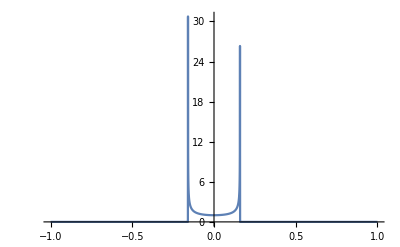

```mathematica
Plot[Re[N[func[Y]]],{Y,-1,1}]
```

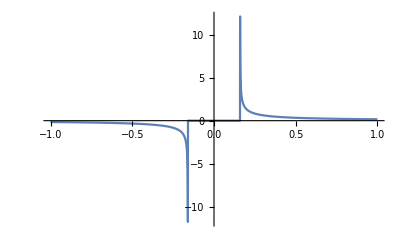

```mathematica
Plot[Im[N[func[Y]]],{Y,-1,1},PlotRange-> All]
```

```mathematica
Clear[func,Y,x];
func[Y_]=Integrate[Exp[-y/2] BesselJ[0, x y] Exp[2 π I y Y],{y,0,∞},Assumptions->{Element[Y,Reals],Element[x,Reals],x>0}]// Simplify
```

(2 ⅈ)/((ⅈ+4 π Y) √(1-(4 x^2)/(ⅈ+4 π Y)^2))

```mathematica
Plot[Re[func[Y] - 2/(√((1-4 π i Y)^2+4 x^2))] /. x-> 1, {Y,0,5}]
```

-Graphics-

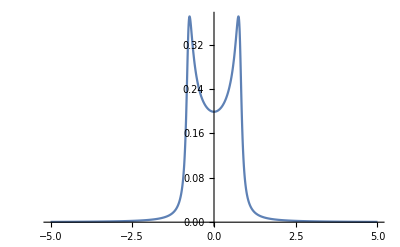

```mathematica
Plot[Re[N[func[Y]]] /. x-> 5,{Y,-5,5},PlotRange-> All]
```

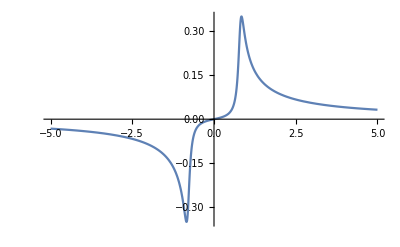

```mathematica
Plot[Im[N[func[Y]]]/. x-> 5,{Y,-5,5},PlotRange-> All]
```

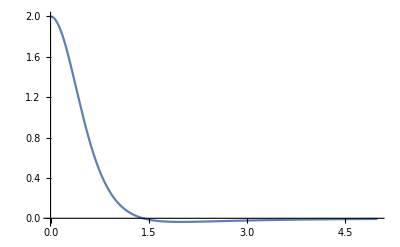

```mathematica
Plot[(2 - x^2)/((1 + x^2)^(5/2)),{x,0,5},PlotRange-> All]
```

```mathematica
f0 = Integrate[Exp[-y/2]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]
```

(2 ⅈ)/(ⅈ+4 π Y)

```mathematica
f1 = Integrate[ y Exp[-y/2]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]
```

-4/(ⅈ+4 π Y)^2

```mathematica
f2 = Integrate[ y^2 Exp[-y/2]Exp[2 π I y Y],{y,0,∞},Assumptions->Element[Y,Reals]]// Simplify
```

2/(1/2-2 ⅈ π Y)^3

Rewrite by hand and so check my results

```mathematica
f0 - 2/(1 - 4 π I Y) // Simplify
```

0

```mathematica
f1 - 4/(1 - 4 π I Y)^2 // Simplify
```

0

```mathematica
f2 - 16/(1 - 4 π I Y)^3 // Simplify
```

0